# Simulation of the max stationary values inDirected Configuration Model (DCM) with power-law in-degree distribution

## Setup

Load the package for simulation.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<DCM`
```

File name of the simulation result data

```mathematica
datafile="max-stationary-data.wl"
```

max-stationary-data.wl

## Parameters

The range of the size of graphs

```mathematica
nmin=1000;nmax=10^4;nstep=10^3;
```

```mathematica
nlist=Range[nmin,nmax,nstep]
```

{1000,2000,3000,4000,5000,6000,7000,8000,9000,10000}

## Degree sequences

## The limit distribution of in-degrees

```mathematica
a0=5/2;r0=2;
```

We will simulate DCM with out-degree fixed to be r0 and in-degree with limit distribution

```mathematica
dist=heavyTailDist[a0,r0]
```

ProbabilityDistribution[Piecewise[{{2/(x^(7/2) (-1+Zeta[5/2])), x≥2}, {(1+Zeta[5/2]-2 Zeta[7/2])/(-1+Zeta[5/2]), x==0}, {0, True}}],{x,0,∞,1}]

The PDF of this distribution

```mathematica
pdf[i_]=PDF[dist,i]
```

Piecewise[{{2/(i^(7/2) (-1+Zeta[5/2])), i≥2}, {(1+Zeta[5/2]-2 Zeta[7/2])/(-1+Zeta[5/2]), i==0}, {0, True}}]

Moments

```mathematica
Moment[dist,1]
```

2

```mathematica
Moment[dist,2]//N
```

9.44325

## The actual bi-degree sequence

Since dist is only a limit, we have create degree sequence which are approximately distributed like it for the simulation.

And we have to decide the max degree for each n. The parameter p0 controls where to cutoff.

```mathematica
p0=1/2;
```

```mathematica
deglistlist=Table[pdf2Deg[pdf,r0,nn,p0],{nn,nmin,nmax,nstep}];
```

We draw some pictures of the in-degrees

```mathematica
histlist=(Histogram[#1⟦1⟧,{0,10,1},"Probability",ImageSize->Medium]&)/@deglistlist;
```

```mathematica
p2=DiscretePlot[pdf[i],{i,0,10,1},PlotRange->Full];
```

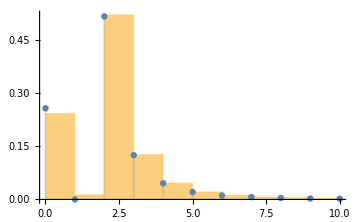
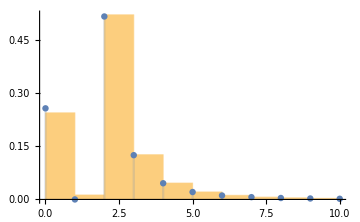
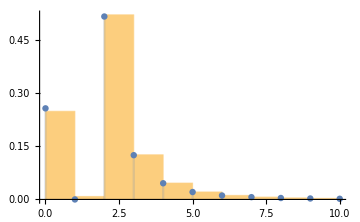
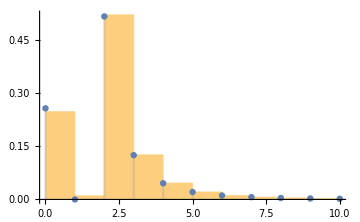
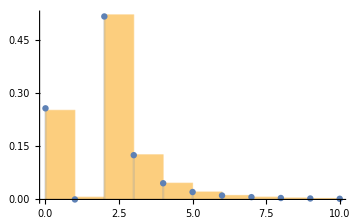
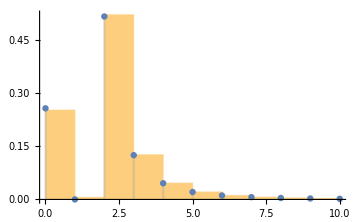
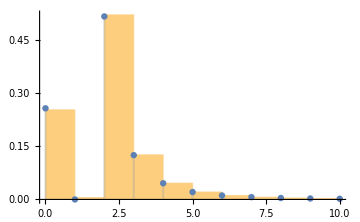
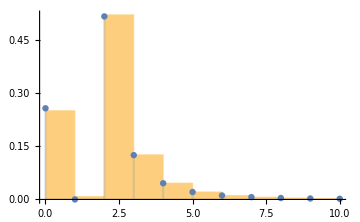

```mathematica
Show[#,p2]&/@histlist
```

As can be seen from the pictures, these degree sequences dos approximates the limit distribution.

## The maximum degrees

The max degrees for each n are

```mathematica
maxdlist=deglistlist[[;;,1,-1]]
```

{15,18,20,22,24,25,26,27,28,29}

So the max degree grows approximately as

```mathematica
data1=Transpose[{maxdlist,nlist}];
```

```mathematica
fit=Fit[data1,{n^(a0+1)},n]
```

0.0772521 n^(7/2)

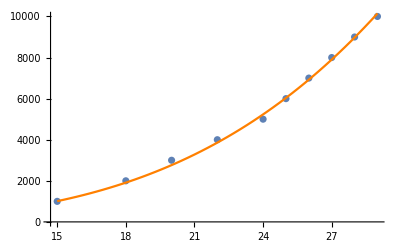

```mathematica
Show[ListPlot[data1],Plot[fit,{n,maxdlist⟦1⟧,maxdlist⟦-1⟧},PlotStyle->Orange]]
```

## Simulation

We will simulate DCM of different sizes and collect data of the maximum stationary distribution and the stationary distribution of the node with max degree.

The number of samples for each n

```mathematica
nsample0=100;
```

```mathematica
Clear[data]
```

```mathematica
data=Monitor[Table[simDCM[pdf,r0,n,p0,nsample0],{n,nmin,nmax, nstep}],n];
```

Save the data to a file.

```mathematica
DeleteFile[datafile]//Quiet;
```

```mathematica
Save[datafile,data]
```

## Analysis

Load simulation data.

```mathematica
Clear[data]
```

```mathematica
Get[datafile];
```

Simulation result is as follows. The column piDelta is the average stationary value of the node with max in-degree Δ^-. The column pimax is the average max stationary value.

```mathematica
result=Dataset[simAnalyze/@data]
```

We see that piDelta is more or less Δ^-/m, while the pimax is larger by a constant factor of about 1.3.

This can also be seen from the picture.

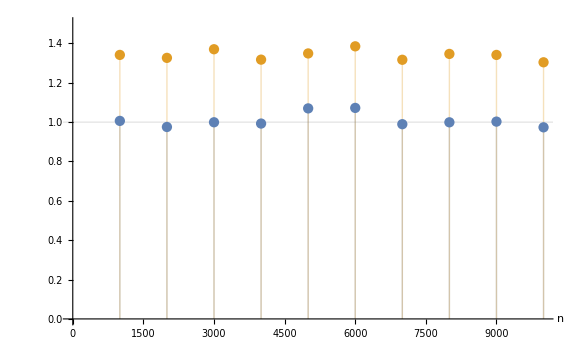

```mathematica
<<MaTeX`
points=Table[{#n,#[col]}&/@result//Normal,{col,{"piDelta/(Δ/m)","pimax/(Δ/m)"}}];
texStyle={FontFamily->"Latin Modern Roman",FontSize->16};
plt=ListPlot[points,BaseStyle->texStyle,PlotRange->{0,1.5},Filling->Axis,ImageSize->Large,AxesLabel->{"n",None},GridLines->{{}, {1}},PlotLegends->(MaTeX[#,Magnification->1.5]&/@{"\\frac{\\pi_{\\Delta^{-}}}{\\Delta^{-}/m}","\\frac{\\pi_{\\max}}{\\Delta{-}/m}"})]
```

```mathematica
Export["simulation.pdf",plt];
```